## Hamilton equations for a basic system

q -> the coordinate 
qd = dq/dt

```mathematica
ham[n_,q_,qd_]:=4 qd^2*Sin[q]-Exp[q]+(n+1/2)*π*Sqrt[qd]; (*test function of the Hamiltonian*)
```

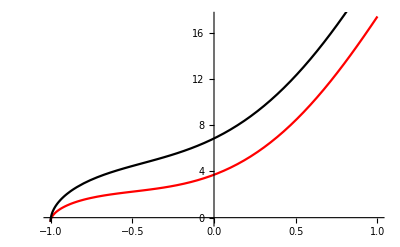

```mathematica
Show[Plot[ham[1,q,q+1],{q,-1,1},PlotStyle->Red],Plot[ham[2,q,q+1],{q,-1,1},PlotStyle->Black]]
```